```mathematica
(*APROKSIMACIJA ŠTEVILA π*)
```

```mathematica
Get[NotebookDirectory[]<>"nakljucneTocke.m"]
```

```mathematica
izracunPi[j_]:= Module[{pie, napaka}, (*Funkcija za izačun približka števila π in absolutne napake*)
{znotrajKroga,zunajKroga}=tocke[j];
pie=N[4 *Length[znotrajKroga]/j];
napaka=Abs[pie-Pi];
{pie, napaka}]
```

```mathematica
n=10000; (*Izberemo maksimalno število naključnih točk pri katerem izračunamo približek števila π*)
For[j=10,j<=n,j*=10, (*Izračunamo približek števila π od n=10 po korakih za *10 do podanega maksimalnega n*)
{pi, odstopek}=izracunPi[j];
Print["Aproksimacija π pri n=",j,": ",pi,"| Abolutna napaka: ", odstopek];
]
```

Aproksimacija π pri n=10: 3.6| Abolutna napaka: 0.458407

Aproksimacija π pri n=100: 2.92| Abolutna napaka: 0.221593

Aproksimacija π pri n=1000: 3.04| Abolutna napaka: 0.101593

Aproksimacija π pri n=10000: 3.1572| Abolutna napaka: 0.0156073

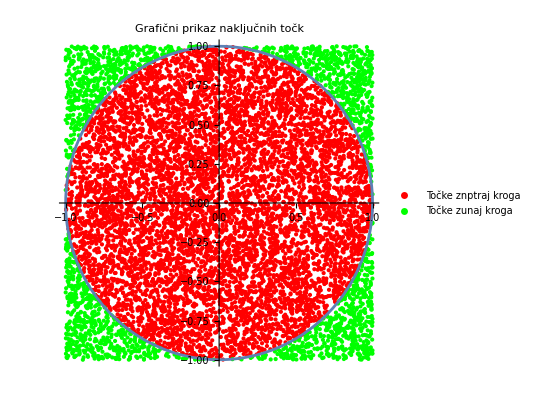

```mathematica
tockeGraf=ListPlot[{znotrajKroga,zunajKroga},PlotLegends->{"Točke znptraj kroga","Točke zunaj kroga"},PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green}}];
kroznica=ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}];
Show[tockeGraf,kroznica,AspectRatio->1,PlotLabel->Style["Grafični prikaz naključnih točk",FontSize->18]]
```

```mathematica
(*RAZVOJ V VRSTO*)
```

```mathematica
f[t_]=Sin[t]*t^2*E^-t;
Manipulate[Plot[{
Evaluate[Normal[Series[Sin[t]*t^2*E^-t,{t,2,k}]]],f[t]},{t,0,4}, PlotRange->{{0,4},{-1,1}},PlotLegends->{"Aproksimacija","Funckcija"}],
{{k,1,"Število členov razvoja"},1,10,1}]
```